```mathematica
<<"/Users/ethan/Desktop/WSS2017/saved_data/editInfo.mx"
<<"/Users/ethan/Desktop/WSS2017/saved_data/compData.mx"
```

```mathematica
urlForm = Flatten @ Table[StringReplace[i, " "-> "_"], {i, Keys[compData]}];
```

```mathematica
header = {"month","Number of edits","IPs","IPs %","Minor edits","Minor edits %"," All edits • IPs • Minor edits"};
EditDates[article_] :=
	Table[
		If[editInfo[article][[2]][[6]][[i]] ≠ header,
			Flatten@{
				DateObject[editInfo[article][[2]][[6]][[i]][[1]]],
				editInfo[article][[2]][[6]][[i]][[2;;]]
			},
			Nothing[]
		],
		{i, 1, Length@editInfo[article][[2]][[6]]}
	];
```

```mathematica
EditDatesPlot[article_] :=
	If[
		Length@EditDates[article] ≥ 25,
		BarChart[
			EditDates[article][[All,2]],
			ChartLabels -> (
				Rotate[DateString@#, Pi/2]&/@(
					ReplacePart[EditDates[article][[All,1 ]],
						List/@Complement[Range@Length@EditDates[article],
							Range[1,Length@EditDates[article], 5]]->""]
				)
			), PlotLabel -> article, ImageSize -> Large
		],
		
		BarChart[
			EditDates[article][[All, 2]],
			ChartLabels -> (
				Rotate[DateString@#, Pi/2]&/@EditDates[article][[All, 1]]
				), PlotLabel -> article, ImageSize -> Large
			]
	]
```

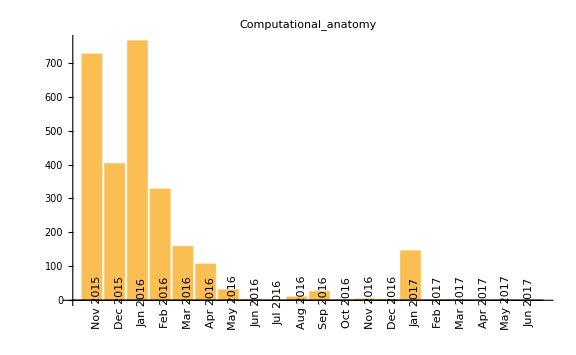

```mathematica
EditDatesPlot["Computational_anatomy"]
```

```mathematica
editDatesGraphs = AssociationMap[EditDatesPlot, urlForm];
```

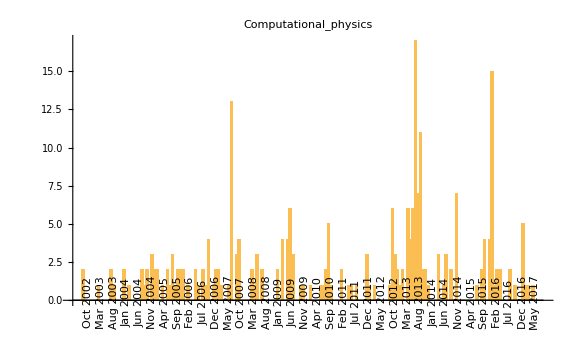

```mathematica
editDatesGraphs["Computational_physics"]
```

```mathematica
DumpSave["/Users/ethan/Desktop/WSS2017/saved_data/editDatesGraphs.mx",editDatesGraphs];
```